```mathematica
SetDirectory["~/jennaproject/data"];
```

```mathematica
kvals=Import["kvals.txt","List"][[1;;420]];
plin=Import["plin.txt","List"][[1;;420]];
b1b2=Import["b1b2.txt","List"][[1;;420]];
b1br=Import["b1br.txt","List"][[1;;420]];
b2b2=Import["b2b2.txt","List"][[1;;420]];
b2br=Import["b2br.txt","List"][[1;;420]];
brbr=Import["brbr.txt","List"][[1;;420]];
tknw=Import["tk_nowiggle.dat","Table"];
```

```mathematica
Dimensions[tknw]
Dimensions[kvals]
```

{3000,2}

{420}

```mathematica
ns=0.966;
```

```mathematica
plinfunc=Interpolation[{kvals,plin}ᵀ];
tknwfunc=Interpolation[tknw];
```

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

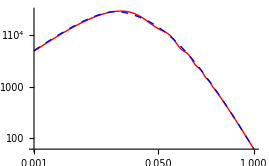

```mathematica
psnwfunc[k_]:=4.0*10^6*k^ns*tknwfunc[k]^2;
LogLogPlot[{plinfunc[k],psnwfunc[k]},{k,0.001,1},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}]
```

```mathematica
b1b2func=Interpolation[{kvals,b1b2}ᵀ];
b1b2nw=Fit[{kvals[[1;;420;;5]],b1b2[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
```

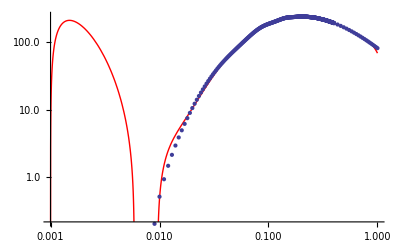

```mathematica
ϕ12=ListLogLogPlot[{kvals,b1b2}ᵀ,PlotStyle->Thick];
ω12=LogLogPlot[b1b2nw,{x,0.001,1},PlotStyle->Red];
Show[ω12,ϕ12]
```

```mathematica
b1brfunc=Interpolation[{kvals,b1br+200}ᵀ];
b1brnw=Fit[{kvals[[1;;420;;5]],b1br[[1;;420;;5]]+200}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
```

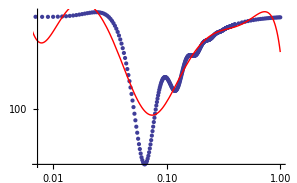

```mathematica
ϕ1r=ListLogLogPlot[{kvals,b1br+200}ᵀ,PlotStyle->Thick];
ω1r=LogLogPlot[b1brnw,{x,0.001,1},PlotStyle->Red];
Show[ϕ1r,ω1r]
```

```mathematica
b2b2func=Interpolation[{kvals,b2b2}ᵀ];
b2b2nw=Fit[{kvals[[1;;420;;5]],b2b2[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^6},x];
```

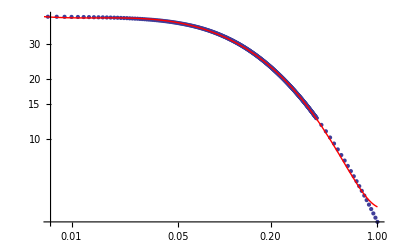

```mathematica
ϕ22=ListLogLogPlot[{kvals,b2b2}ᵀ,PlotStyle->Thick];
ω22=LogLogPlot[b2b2nw,{x,0.001,1},PlotStyle->Red];
Show[ ϕ22,ω22]
```

```mathematica
b2brfunc=Interpolation[{kvals,b2br}ᵀ];
b2brnw=Fit[{kvals[[1;;420;;5]],b2br[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
```

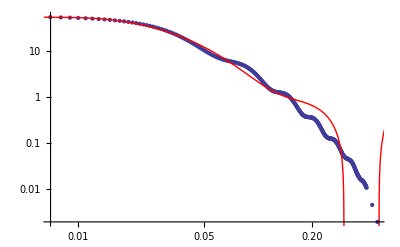

```mathematica
ϕ2r=ListLogLogPlot[{kvals,b2br}ᵀ,PlotStyle->Thick];
ω2r=LogLogPlot[b2brnw,{x,0.001,1},PlotStyle->Red];
Show[ ϕ2r,ω2r]
```

```mathematica
brbrfunc=Interpolation[{kvals,brbr}ᵀ];
brbrnw=Fit[{kvals[[1;;420;;5]],brbr[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
```

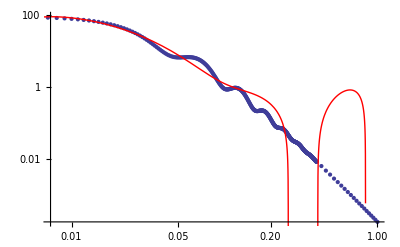

```mathematica
ϕrr=ListLogLogPlot[{kvals,brbr}ᵀ,PlotStyle->Thick];
ωrr=LogLogPlot[brbrnw,{x,0.001,1},PlotStyle->Red];
Show[ ϕrr,ωrr]
```

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

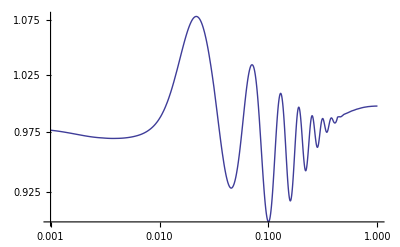

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

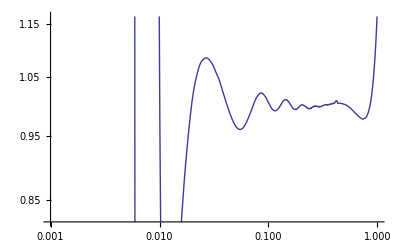

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

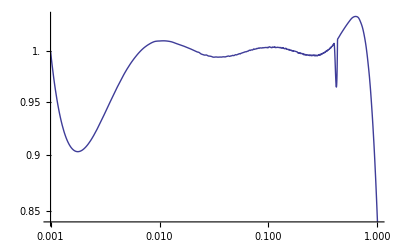

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

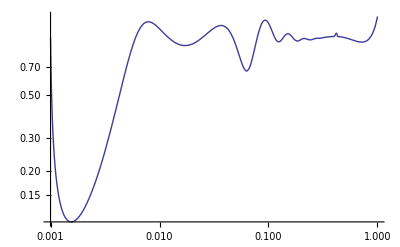

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

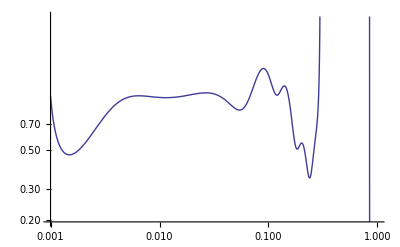

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

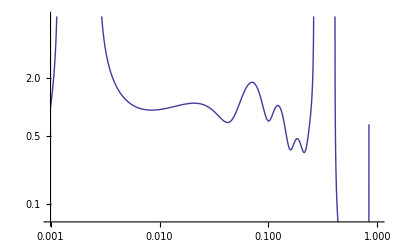

```mathematica
LogLogPlot[plinfunc[x]/psnwfunc[x],{x,0.001,1},PlotStyle->Thick]
LogLogPlot[b1b2func[x]/b1b2nw,{x,0.001,1},PlotStyle->Thick]
LogLogPlot[b2b2func[x]/b2b2nw,{x,0.001,1},PlotStyle->Thick]
LogLogPlot[b1brfunc[x]/b1brnw,{x,0.001,1},PlotStyle->Thick]
LogLogPlot[b2brfunc[x]/b2brnw,{x,0.001,1},PlotStyle->Thick]
LogLogPlot[brbrfunc[x]/brbrnw,{x,0.001,1},PlotStyle->Thick]
```